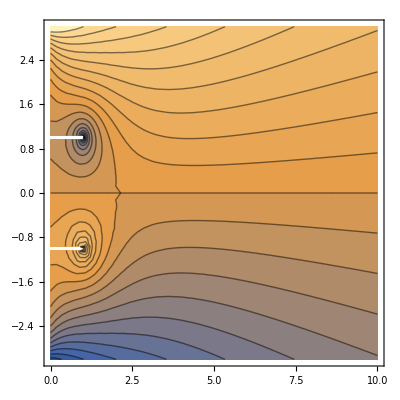

```mathematica
(*wΓ[z_,z0_,Γ_]=Γ/(2 ⅈ π)(Log[z-z0]-Log[z-z0*]);
wQ[z_,z0_,Q_]=Q/(2 π)(Log[z-z0]+Log[z-z0*]);*)
w0[z_,z0_,W_,ι_]=(W √ι)/(2  π)(ι Log[z-z0]+Log[z-z0*]);
w[z_]=w0[z,-.5-3ⅈ,3,1] + w0[z,1-ⅈ,1,-1];
ContourPlot[Im@w[x+ⅈ y],{x,0,10},{y,-3,3},Contours->20]
```

```mathematica
D[w0[z,z0,M,ι],z]
```

(M √ι (ι/(z-z0)+1/(z-Conjugate[z0])))/(2 π)